```mathematica
ClearAll["`*"]
(*$PreRead=(#/.
s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`12."&);*)
```

```mathematica
order = 3;
kmin = 0.1; R = 10; Z=1; c = 137; k =-1;
nnode = 10;
knot = Table[ kmin(R/kmin)^((i-1)/(nnode-1)), {i,1, nnode}]
n = Length[knot]-order-2
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
v=-Z/r;
```

{0.1,0.16681,0.278256,0.464159,0.774264,1.29155,2.15443,3.59381,5.99484,10.}

5

```mathematica
Cmat =  Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Cmat // Dimensions, SymmetricMatrixQ[Cmat]}
Cmat // MatrixForm
```

{{4,4},True}

(0.13689 | 0.0823695 | 0.00915668 | 0.0000810899
0.0823695 | 0.228347 | 0.137401 | 0.0152743
0.00915668 | 0.137401 | 0.380905 | 0.229198
0.0000810899 | 0.0152743 | 0.229198 | 0.635388)

```mathematica
Dmat =  Evaluate[Table[Integrate[ϕi[r,ai] D[ϕi[r,aj], r],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Dmat // Dimensions, SymmetricMatrixQ[Dmat]}
Dmat // MatrixForm
```

{{4,4},False}

(6.73434×10^-17 | 0.353056 | 0.0718262 | 0.00109732
-0.353056 | -2.10931×10^-17 | 0.353056 | 0.0718262
-0.0718262 | -0.353056 | -7.9207×10^-17 | 0.353056
-0.00109732 | -0.0718262 | -0.353056 | 7.40924×10^-17)

```mathematica
Vmat = Evaluate[Table[Integrate[ϕi[r,ai] v ϕi[r,aj], {r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Vmat // Dimensions, SymmetricMatrixQ[Vmat]}
N[Vmat, 12] // MatrixForm
```

{{4,4},True}

(-0.251294 | -0.119301 | -0.0108157 | -0.000079063
-0.119301 | -0.251294 | -0.119301 | -0.0108157
-0.0108157 | -0.119301 | -0.251294 | -0.119301
-0.000079063 | -0.0108157 | -0.119301 | -0.251294)

```mathematica
Kmat = Evaluate[Table[Integrate[ϕi[r,ai] k/r ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Kmat // Dimensions, SymmetricMatrixQ[Kmat]}
Kmat // MatrixForm
```

{{4,4},True}

(-0.251294 | -0.119301 | -0.0108157 | -0.000079063
-0.119301 | -0.251294 | -0.119301 | -0.0108157
-0.0108157 | -0.119301 | -0.251294 | -0.119301
-0.000079063 | -0.0108157 | -0.119301 | -0.251294)

```mathematica
Aprime = Table[If[k > 0, 
2 c^2 KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[i,2n-2],
c KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[j,2n-2]
],{i,1,2n-2},{j,1,2n-2}];
{Aprime // Dimensions, SymmetricMatrixQ[Aprime]}
Aprime // MatrixForm
```

{{8,8},True}

(137 | 0 | 0 | 0 | -137/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 137/2 | 0 | 0 | 0 | 0
-137/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -137/2)

```mathematica
Amat = ArrayFlatten[{{Vmat, c (Dmat-Kmat)}, {-c(Dmat+Kmat), Vmat-2c^2 Cmat}}] + Aprime;
{Amat // Dimensions, SymmetricMatrixQ[Amat]}
N[Amat] // MatrixForm
```

{{8,8},True}

(136.749 | -0.119301 | -0.0108157 | -0.000079063 | -34.0728 | 64.7129 | 11.3219 | 0.161165
-0.119301 | -0.251294 | -0.119301 | -0.0108157 | -32.0244 | 34.4272 | 64.7129 | 11.3219
-0.0108157 | -0.119301 | -0.251294 | -0.119301 | -8.35843 | -32.0244 | 34.4272 | 64.7129
-0.000079063 | -0.0108157 | -0.119301 | 68.2487 | -0.139501 | -8.35843 | -32.0244 | 34.4272
-34.0728 | -32.0244 | -8.35843 | -0.139501 | -5138.83 | -3092.11 | -343.734 | -3.04403
64.7129 | 34.4272 | -32.0244 | -8.35843 | -3092.11 | -8571.93 | -5157.86 | -573.376
11.3219 | 64.7129 | 34.4272 | -32.0244 | -343.734 | -5157.86 | -14298.7 | -8603.76
0.161165 | 11.3219 | 64.7129 | 34.4272 | -3.04403 | -573.376 | -8603.76 | -23919.9)

```mathematica
Bmat = ArrayFlatten[{{Cmat,0}, {0,Cmat}}];
{Bmat // Dimensions, SymmetricMatrixQ[Bmat]}
N[Bmat] // MatrixForm
```

{{8,8},True}

(0.13689 | 0.0823695 | 0.00915668 | 0.0000810899 | 0. | 0. | 0. | 0.
0.0823695 | 0.228347 | 0.137401 | 0.0152743 | 0. | 0. | 0. | 0.
0.00915668 | 0.137401 | 0.380905 | 0.229198 | 0. | 0. | 0. | 0.
0.0000810899 | 0.0152743 | 0.229198 | 0.635388 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.13689 | 0.0823695 | 0.00915668 | 0.0000810899
0. | 0. | 0. | 0. | 0.0823695 | 0.228347 | 0.137401 | 0.0152743
0. | 0. | 0. | 0. | 0.00915668 | 0.137401 | 0.380905 | 0.229198
0. | 0. | 0. | 0. | 0.0000810899 | 0.0152743 | 0.229198 | 0.635388)

```mathematica
energy = Sort[Eigenvalues[N[{Amat, Bmat},30]]]
```

{-37686.6,-37551.3,-37540.8,-37539.4,0.243577,3.5911,145.648,1372.57}

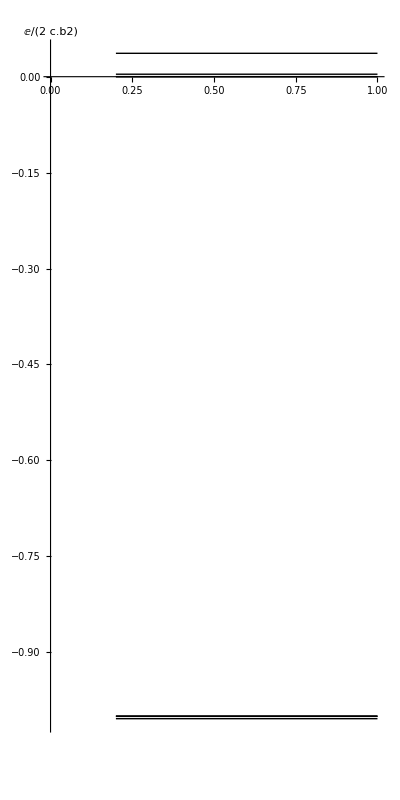

```mathematica
Plot[energy/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
```

#### Plot fortran result

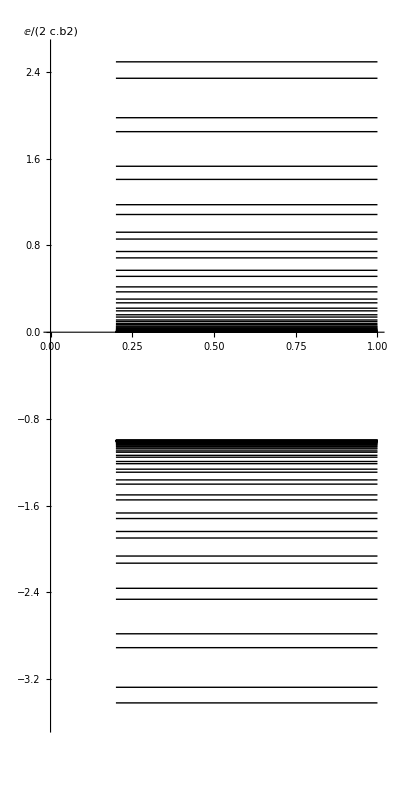

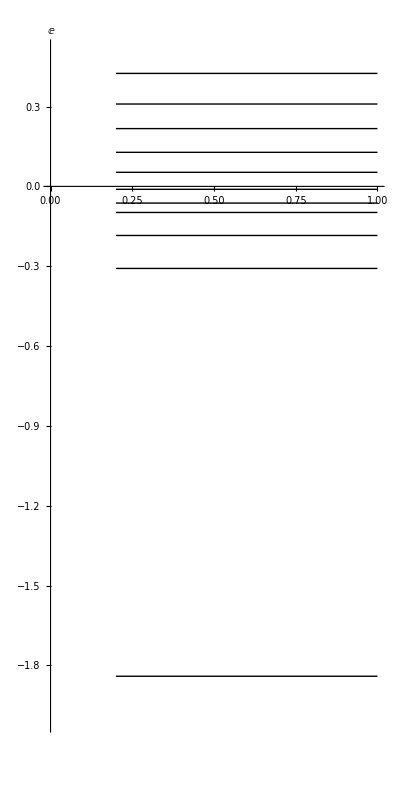

```mathematica
feigval =Import["/home/mathispanet/Documents/Fortran-BSpline/eigenvalues.dat", "CSV"];
Plot[feigval/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
Plot[feigval,{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},{-2, 0.5}},PlotRangeClipping->True, AxesLabel->E]
```